Define the surface interesctions
y direction along the cyl
x axis of tilt
surface of the mcp is tilted by angle α (would be z,x plane for zero tilt)
z=y 1/Tan[α]=y Sin[α]/Cos[α]
x=free
parametric cyl (u,v)
x=Cos[u]
y=v
z=Sin[u]
the intersection is thus
x=Cos[u]
y=z Sin[α]/Cos[α]=Sin[u] Sin[α]/Cos[α]
z=Sin[u]
Rotate into the plane of the mcp x’,y’,z’ with the rotation
x’=x
y’=  y cos(α) -z sin(α)
z’= y sin(α) + z cos(α

apply the rotation to the intersection
x’=Cos[u]
y’=(Sin[u] Sin[α]/Cos[α])Cos[α]-(Sin[u])Sin[α]
z’=(Sin[u] Sin[α]/Cos[α])Sin[α]+(Sin[u])Cos[α]
simplify
x’=Cos[u]
y’=0
z’=(Sin[u] (Sin[α])^2)/Cos[α]+Sin[u]Cos[α]
again
x’=Cos[u]
y’=0
z’=Sin[u] ((Sin[α])^2/Cos[α]+Cos[α])
this is then an elipse with radius (1, ((Sin[α])^2/Cos[α]+Cos[α])) in x,y respectively
The area should be
A= π ((Sin[α])^2/Cos[α]+Cos[α])

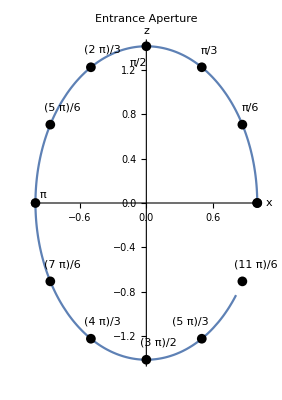

```mathematica
xpos[u_]=Cos[u];
zpos[u_]=Sin[u] ((Sin[α])^2/Cos[α]+Cos[α]);
zmax[αvar_]:=2*zpos[π/2]/.α->αvar;
areaEllipse[αvar_]=π((Sin[α])^2/Cos[α]+Cos[α])/.α->αvar;
eccenEllipse[αvar_]=√(1-1^2/(((Sin[αvar])^2/Cos[αvar]+Cos[αvar])^2));
cicumEllipse[αvar_]=4 ((Sin[αvar])^2/Cos[αvar]+Cos[αvar])EllipticE[π/2,(eccenEllipse[αvar])^2];
alphaTemp=45*π/180;

Show[
ParametricPlot[{xpos[a],zpos[a]}/.α->alphaTemp,{a,0π,1.8π},AxesLabel->{"x","z"},PlotLabel->"Entrance Aperture"],
ListPlot[Table[Labeled[{xpos[a],zpos[a]},a],{a,0,2Pi,Pi/6}]/.α->alphaTemp,
PlotStyle->Black,PlotMarkers->{Automatic,Medium}]/.Line->Point,
PlotRangePadding->0.2
]
```

```mathematica
alphaTemp=45*π/180;
Manipulate[Show[ParametricPlot[{xpos[a],zpos[a]}/.α->alphaTemp,{a,-π,π},PlotLabel->b,PlotRange->{{-1.5,1.5},{-1,1}*1.1*zmax[alphaTemp]}],ParametricPlot[{xpos[a],zpos[a]+b}/.α->alphaTemp,{a,-π,π},AxesLabel->{"x","z"},PlotLabel->b]],{b,-0.1*zmax[alphaTemp],zmax[alphaTemp]}]
```

## Intersection Points

Now try to solve for the intersection points of two of these eclipse with one offset in z by an amount g

```mathematica
intersectionpts=Solve[{xpos[u]==xpos[q], 
zpos[u]==zpos[q]+g},{q,u}]
```

{{q→ConditionalExpression[ArcTan[-(√(-g^2+4 Cos[α]^2+8 Sin[α]^2+4 Sin[α]^2 Tan[α]^2))/(2 √(Cos[α]^2+2 Sin[α]^2+Sin[α]^2 Tan[α]^2)),-g/(2 (Cos[α]+Sin[α] Tan[α]))]+2 π C[1],C[1]∈ℤ],u→ConditionalExpression[ArcTan[-(√(-g^2+4 Cos[α]^2+8 Sin[α]^2+4 Sin[α]^2 Tan[α]^2))/(2 √(Cos[α]^2+2 Sin[α]^2+Sin[α]^2 Tan[α]^2)),g/(2 (Cos[α]+Sin[α] Tan[α]))]+2 π C[2],C[2]∈ℤ]},{q→ConditionalExpression[ArcTan[(√(-g^2+4 Cos[α]^2+8 Sin[α]^2+4 Sin[α]^2 Tan[α]^2))/(2 √(Cos[α]^2+2 Sin[α]^2+Sin[α]^2 Tan[α]^2)),-g/(2 (Cos[α]+Sin[α] Tan[α]))]+2 π C[1],C[1]∈ℤ],u→ConditionalExpression[ArcTan[(√(-g^2+4 Cos[α]^2+8 Sin[α]^2+4 Sin[α]^2 Tan[α]^2))/(2 √(Cos[α]^2+2 Sin[α]^2+Sin[α]^2 Tan[α]^2)),g/(2 (Cos[α]+Sin[α] Tan[α]))]+2 π C[2],C[2]∈ℤ]}}

Remove the 2π periodicity in the solution, and give the polar cord of intersections in both circles
We want the anglular cord of the ellipse that moves up and should converge to (3 π)/2  = -π/2at zmax[alphaTemp]

```mathematica
intersectionpts[[1,2,2]]
```

ConditionalExpression[ArcTan[-(√(-d^2+4 Cos[α]^2+8 Sin[α]^2+4 Sin[α]^2 Tan[α]^2))/(2 √(Cos[α]^2+2 Sin[α]^2+Sin[α]^2 Tan[α]^2)),d/(2 (Cos[α]+Sin[α] Tan[α]))]+2 π C[2],C[2]∈ℤ]

```mathematica
IntersectPts={{intersectionpts[[2,1,2]]/.C[1]->0,intersectionpts[[1,1,2]]/.C[1]->0},{intersectionpts[[2,2,2]]/.C[2]->0,intersectionpts[[1,2,2]]/.C[2]->0}}
```

{{ArcTan[(√(-g^2+4 Cos[α]^2+8 Sin[α]^2+4 Sin[α]^2 Tan[α]^2))/(2 √(Cos[α]^2+2 Sin[α]^2+Sin[α]^2 Tan[α]^2)),-g/(2 (Cos[α]+Sin[α] Tan[α]))],ArcTan[-(√(-g^2+4 Cos[α]^2+8 Sin[α]^2+4 Sin[α]^2 Tan[α]^2))/(2 √(Cos[α]^2+2 Sin[α]^2+Sin[α]^2 Tan[α]^2)),-g/(2 (Cos[α]+Sin[α] Tan[α]))]},{ArcTan[(√(-g^2+4 Cos[α]^2+8 Sin[α]^2+4 Sin[α]^2 Tan[α]^2))/(2 √(Cos[α]^2+2 Sin[α]^2+Sin[α]^2 Tan[α]^2)),g/(2 (Cos[α]+Sin[α] Tan[α]))],ArcTan[-(√(-g^2+4 Cos[α]^2+8 Sin[α]^2+4 Sin[α]^2 Tan[α]^2))/(2 √(Cos[α]^2+2 Sin[α]^2+Sin[α]^2 Tan[α]^2)),g/(2 (Cos[α]+Sin[α] Tan[α]))]}}

```mathematica
IntersectPts
```

{{ArcTan[(√(-d^2+4 Cos[α]^2+8 Sin[α]^2+4 Sin[α]^2 Tan[α]^2))/(2 √(Cos[α]^2+2 Sin[α]^2+Sin[α]^2 Tan[α]^2)),-d/(2 (Cos[α]+Sin[α] Tan[α]))],ArcTan[-(√(-d^2+4 Cos[α]^2+8 Sin[α]^2+4 Sin[α]^2 Tan[α]^2))/(2 √(Cos[α]^2+2 Sin[α]^2+Sin[α]^2 Tan[α]^2)),-d/(2 (Cos[α]+Sin[α] Tan[α]))]},{ArcTan[(√(-d^2+4 Cos[α]^2+8 Sin[α]^2+4 Sin[α]^2 Tan[α]^2))/(2 √(Cos[α]^2+2 Sin[α]^2+Sin[α]^2 Tan[α]^2)),d/(2 (Cos[α]+Sin[α] Tan[α]))],ArcTan[-(√(-d^2+4 Cos[α]^2+8 Sin[α]^2+4 Sin[α]^2 Tan[α]^2))/(2 √(Cos[α]^2+2 Sin[α]^2+Sin[α]^2 Tan[α]^2)),d/(2 (Cos[α]+Sin[α] Tan[α]))]}}

Check that they give the right answer in the limit of zero displacement

```mathematica
Limit[IntersectPts,d->0]
```

{{0,π},{0,π}}

```mathematica
FullSimplify[IntersectPts/.d->zmax[α]]
```

{{-π/2,-π/2},{π/2,π/2}}

Show that they are anti-symmetric, numerically

Try a simplify

```mathematica
alphaTemp=45*π/180;

Manipulate[
Module[{gtmp},
gtmp=gfac*zmax[alphaTemp];
Show[
ParametricPlot[{xpos[a],zpos[a]}/.α->alphaTemp,{a,-π,π},PlotLabel->StringForm["``.,``.,``.",bfac,N[Intersect1/.{α->alphaTemp,d->b},2],N[Intersect2/.{α->alphaTemp,d->b},2]],
PlotRange->{{-1.5,1.5},{-1,1}*zmax[alphaTemp]}],
ParametricPlot[{xpos[a],zpos[a]+gtmp}/.α->alphaTemp,{a,-π,π}],
ListPlot[{
Labeled[{xpos[IntersectPts[[1,1]]],zpos[IntersectPts[[1,1]]]+g},"11"],
{xpos[IntersectPts[[1,2]]],zpos[IntersectPts[[1,2]]]+g},
{xpos[IntersectPts[[2,1]]],zpos[IntersectPts[[2,1]]]},
{xpos[IntersectPts[[2,2]]],zpos[IntersectPts[[2,2]]]}
}/.{α->alphaTemp,g->gtmp},PlotStyle->{Red,PointSize[Large]}],
ParametricPlot[{xpos[a],zpos[a]+gtmp}/.α->alphaTemp,{a,IntersectPts[[1,1]]/.{α->alphaTemp,g->gtmp},IntersectPts[[1,2]]/.{α->alphaTemp,g->gtmp}},PlotStyle->{Red}],
ParametricPlot[{xpos[a],zpos[a]}/.α->alphaTemp,{a,IntersectPts[[2,1]]/.{α->alphaTemp,g->gtmp},IntersectPts[[2,2]]/.{α->alphaTemp,g->gtmp}},PlotStyle->{Green}]
]],
{gfac,0.001,0.9999}
]
```

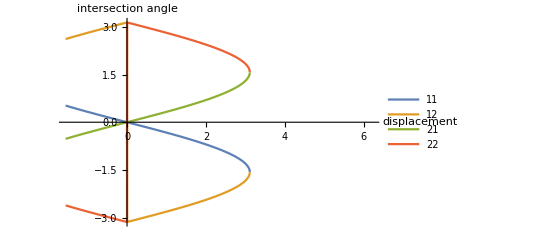

```mathematica
alphaTemp=50*π/180;
Plot[{IntersectPts[[1,1]]/.{α->alphaTemp,g->x},
IntersectPts[[1,2]]/.{α->alphaTemp,g->x},
IntersectPts[[2,1]]/.{α->alphaTemp,g->x},
IntersectPts[[2,2]]/.{α->alphaTemp,g->x}},{x,-0.5*zmax[alphaTemp],2*zmax[alphaTemp]},PlotLegends->{"11","12","21","22"},AxesLabel->{"displacement","intersection angle"}]
```

## Surface area integral

Find the area between the x axis and the circle arc between intersection points
A=∫y(x)ⅆx 
do a change of var
x=cos(ϕ)
dx/dϕ=-sin(ϕ)
A=∫y(ϕ)(-sin(ϕ)) ⅆϕ

0

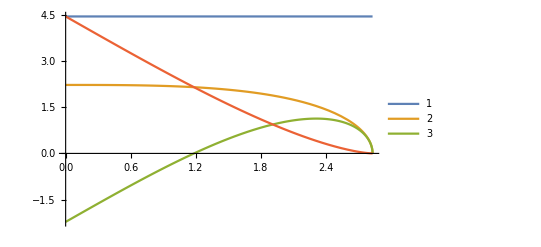

```mathematica
AreaPart1=areaEllipse[α];
offsetz=0
AreaPart2=Integrate[(zpos[ϕ]+offsetz)* D[xpos[ϕ],ϕ]  ,{ϕ,IntersectPts[[2,2]],IntersectPts[[2,1]]}];
AreaPart3=Integrate[((g+zpos[ϕ]+offsetz) * D[xpos[ϕ],ϕ])  ,{ϕ,IntersectPts[[1,2]],IntersectPts[[1,1]]}];
alphaTemp=45*π/180;
Plot[{AreaPart1/.α->alphaTemp,AreaPart2/.α->alphaTemp,AreaPart3/.α->alphaTemp,(AreaPart2-AreaPart3)/.α->alphaTemp},{g,0,zmax[alphaTemp]},PlotLegends->{"1","2","3"}]
```

```mathematica
assum={α∈Reals,α>0,α<π/2,g>0,g<zmax[α]}
```

{α∈ℝ,α>0,α<π/2,g>0,g<2 (Cos[α]+Sin[α] Tan[α])}

```mathematica
AreaBetweenArcs=areaEllipse[α]-(     Integrate[(zpos[ϕ]+zmax[α] )* D[xpos[ϕ],ϕ]  ,{ϕ,IntersectPts[[2,2]],IntersectPts[[2,1]]}]-
								Integrate[((g+zpos[ϕ]+zmax[α]) * D[xpos[ϕ],ϕ])  ,{ϕ,IntersectPts[[1,2]],IntersectPts[[1,1]]}]     );
AreaBetweenArcs=Simplify[AreaBetweenArcs,Assumptions->assum]
AreaBetweenArcsPerp=FullSimplify[AreaBetweenArcs/.α->0,Assumptions->assum]
```

1/2 Sec[α] (ArcTan[-√(-g^2+4 Sec[α]^2),-g]-ArcTan[-√(-g^2+4 Sec[α]^2),g]-ArcTan[√(-g^2+4 Sec[α]^2),-g]+ArcTan[√(-g^2+4 Sec[α]^2),g]+2 π Cos[α]^2+g Cos[α]^2 √(-g^2+4 Sec[α]^2)+2 π Sin[α]^2)

1/2 (g √(4-g^2)+2 π+ArcTan[-√(4-g^2),-g]-ArcTan[-√(4-g^2),g]-ArcTan[√(4-g^2),-g]+ArcTan[√(4-g^2),g])

```mathematica
dareadg=FullSimplify[D[AreaBetweenArcs,g],Assumptions->assum]
```

Cos[α] √(-g^2+4 Sec[α]^2)

```mathematica
NormFac=Integrate[dareadg,{g,0,zmax[α]},Assumptions->assum]
```

π Sec[α]

```mathematica
densityg=FullSimplify[dareadg/NormFac,Assumptions->assum]
```

(Cos[α]^2 √(-g^2+4 Sec[α]^2))/π

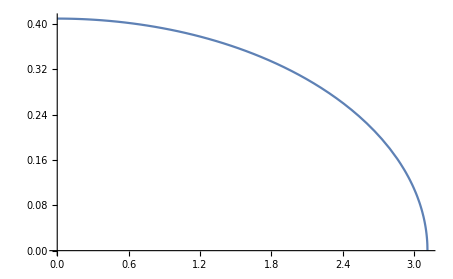

```mathematica
alphaTemp=50*π/180;
Plot[densityg/.{α->alphaTemp,g->x},{x,0,zmax[alphaTemp]}]
```

```mathematica
alphaTemp=50*π/180;

NIntegrate[densityg/.{α->alphaTemp},{g,0,zmax[alphaTemp]}]
```

1.

```mathematica
Integrate[densityg,{g,0,zmax}]
```

$Aborted

## Transform Density

Transform the density distribution from a distribution in g to a distribution in delay

```mathematica
tmax=1/v 2/Sin[α]
```

(2 Csc[α])/v

Now lets do a change of variables  as per https://en.wikipedia.org/wiki/Probability_density_function
from a function in g to a function in tdelay
-Graphics-

t_delay=fun(g)
g=fun^-1(t_delay)
where h is the travel distance, t_delay is the delay time, v is the velocity
tan(α)=g/h
h=g/(tan(α))
t_delay=1/v g/(tan(α))
g= t_delay v tan(α)=
fun^-1=t_delay  v  tan(α)
d/dt_delay fun^-1= v  tan(α)
f_h(h)= v  tan(α)   f_g(   t_delay  v  tan(α)  )

```mathematica
tdelayfun=1/v g/Tan[α];
gfun= Subscript[t, delay]   v   Tan[α] ;
```

```mathematica
EqualTo[Simplify[tdelayfun/.g->zmax[α]]][tmax/.rpore->1]
```

True

```mathematica
densitytdelay=FullSimplify[v Tan[α] (densityg/.g->gfun),Assumptions->{α∈Reals,Subscript[t, delay]∈Reals,α>0,α<π/2,Subscript[t, delay]>0,Subscript[t, delay]<tmax}]
```

(v Sin[α] √(4-v^2 Sin[α]^2 t_delay^2))/π

```mathematica
Integrate[densitytdelay,{Subscript[t, delay],0,tmax},Assumptions->{α∈Reals,Subscript[t, delay]∈Reals,α>0,α<π/2,Subscript[t, delay]>0,Subscript[t, delay]<tmax}]
```

$Aborted

```mathematica
alphaTemp=0.1*π/180;

NIntegrate[densitytdelay/.{α->alphaTemp,v->1,rpore->1},{Subscript[t, delay],0,tmax/.{v->1,rpore->1,α-> alphaTemp}}]
alphaTemp=45*π/180;
NIntegrate[densitytdelay/.{α->alphaTemp,v->1,rpore->1},{Subscript[t, delay],0,tmax/.{v->1,rpore->1,α-> alphaTemp}}]
```

1.

1.

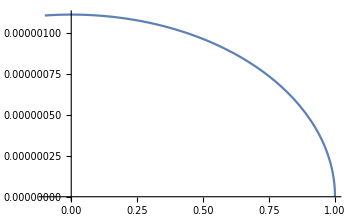

```mathematica
alphaTemp=0.0001*π/180;
tmax/.{α->alphaTemp,v->1,rpore->1};
Plot[densitytdelay/.{Subscript[t, delay]->x*tmax/.{α->alphaTemp,v->1,rpore->1},α->alphaTemp,v->1,rpore->1},{x,0-0.1,1}]
```

```mathematica
guessexpression=FullSimplify[(4 √(tmax^2-Subscript[t, delay]^2))/(π tmax^2)/.{v->1,rpore->1},Assumptions->{α∈Reals,Subscript[t, delay]∈Reals,α>0,α<π/2,Subscript[t, delay]>0,Subscript[t, delay]<tmax}]
```

(Sin[α]^2 √(4 Csc[α]^2-t_delay^2))/π

```mathematica
alphaTemp=0.1*π/180;

NIntegrate[guessexpression/.{α->alphaTemp,v->1,rpore->1},{Subscript[t, delay],0,tmax/.{v->1,rpore->1,α-> alphaTemp}}]
alphaTemp=45*π/180;
NIntegrate[guessexpression/.{α->alphaTemp,v->1,rpore->1},{Subscript[t, delay],0,tmax/.{v->1,rpore->1,α-> alphaTemp}}]
```

1.

1.

```mathematica
FullSimplify[densitytdelay]
```

(v Sin[α] √(4-v^2 Sin[α]^2 t_delay^2))/π

```mathematica
alphaTemp=45*π/180;
guessdiference=FullSimplify[(densitytdelay-guessexpression)/.{v->1}]
FullSimplify[guessdiference,Assumptions->{α∈Reals,Subscript[t, delay]∈Reals,α>0,α<π/2,Subscript[t, delay]>0,Subscript[t, delay]<tmax}]
N[guessdiference/.{α->0.1,Subscript[t, delay]->0.4}]
```

(-Sin[α]^2 √(4 Csc[α]^2-t_delay^2)+Sin[α] √(4-Sin[α]^2 t_delay^2))/π

(-Sin[α]^2 √(4 Csc[α]^2-t_delay^2)+Sin[α] √(4-Sin[α]^2 t_delay^2))/π

0.

## Statistics

```mathematica
densitytdelay
```

(v Sin[α] √(4-v^2 Sin[α]^2 t_delay^2))/π

```mathematica
Integrate[densitytdelay,{Subscript[t, delay],0,tmax},Assumptions->{α∈Reals,Subscript[t, delay]∈Reals,α>0,α<π/2,Subscript[t, delay]>0,Subscript[t, delay]<tmax,v∈Reals,v>0}]
```

1

```mathematica
meandelay=Integrate[Subscript[t, delay] densitytdelay,{Subscript[t, delay],0,tmax},Assumptions->{α∈Reals,Subscript[t, delay]∈Reals,α>0,α<π/2,Subscript[t, delay]>0,Subscript[t, delay]<tmax,v∈Reals,v>0}]
```

(8 Csc[α])/(3 π v)

```mathematica
meandelayreduced=FullSimplify[meandelay/tmax,Assumptions->{α∈Reals,Subscript[t, delay]∈Reals,α>0,α<π/2,Subscript[t, delay]>0,Subscript[t, delay]<tmax,v∈Reals,v>0}]
```

4/(3 π)

```mathematica
N[meandelayreduced]
```

0.424413

```mathematica
stddelay=√(Integrate[(Subscript[t, delay])^2 densitytdelay,{Subscript[t, delay],0,tmax},Assumptions->{α∈Reals,Subscript[t, delay]∈Reals,α>0,α<π/2,Subscript[t, delay]>0,Subscript[t, delay]<tmax,v∈Reals,v>0}]-meandelay^2)
```

√(Csc[α]^2/v^2-(64 Csc[α]^2)/(9 π^2 v^2))

```mathematica
stddelayReduced=FullSimplify[stddelay/tmax,Assumptions->{α∈Reals,Subscript[t, delay]∈Reals,α>0,α<π/2,Subscript[t, delay]>0,Subscript[t, delay]<tmax,v∈Reals,v>0}]
```

(√(-64+9 π^2))/(6 π)

```mathematica
N[stddelayReduced]
```

0.264336

```mathematica
cdf=Integrate[densitytdelay,{Subscript[t, delay],0,tvar},Assumptions->{α∈Reals,Subscript[t, delay]∈Reals,α>0,α<π/2,Subscript[t, delay]>0,Subscript[t, delay]<tmax,tvar∈Reals,tvar>0,tvar<tmax,v∈Reals,v>0}]
```

(8 ArcSin[1/2 tvar v Sin[α]]+√2 tvar v √(8-tvar^2 v^2+tvar^2 v^2 Cos[2 α]) Sin[α])/(4 π)

```mathematica
cdfreduced=FullSimplify[cdf/.tvar->tmax tmaxfrac,Assumptions->{α∈Reals,tvar∈Reals,α>0,α<π/2,tvar>0,tvar<tmax,v∈Reals,v>0}]
```

(2 (tmaxfrac √(1-tmaxfrac^2)+ArcSin[tmaxfrac]))/π

```mathematica
Expand[cdfreduced]
```

(2 tmaxfrac √(1-tmaxfrac^2))/π+(2 ArcSin[tmaxfrac])/π

```mathematica
FindRoot[cdfreduced-1/2,{tmaxfrac,0.5}]
```

{tmaxfrac→0.403973}

```mathematica
Solve[cdfreduced==1/2]
```

$Aborted

```mathematica
FullSimplify[cdf/.{α->alphaTemp1,v->vtemp1,tvar->0*(tmax/.{α->alphaTemp1,v->vtemp1})}]
FullSimplify[cdf/.{α->alphaTemp1,v->vtemp1,tvar->(tmax/.{α->alphaTemp1,v->vtemp1})}]
N[FullSimplify[cdf/.{α->alphaTemp1,v->vtemp1,tvar->2 (tmax/.{α->alphaTemp1,v->vtemp1})}]]
```

0

1

1.+1.36691 ⅈ

1

10

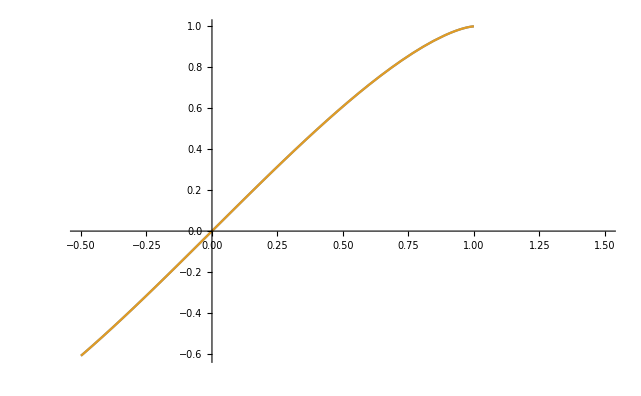

```mathematica
alphaTemp1=80*π/180;
alphaTemp2=0.1*π/180;
vtemp1=1
vtemp2=10
Plot[{(cdfreduced/.{α->alphaTemp1,v->vtemp1}),
(cdfreduced/.{α->alphaTemp2,v->vtemp2})},{tmaxfrac,-0.5,1.5}]
```

```mathematica
cdf=(v ((tvar √(8-tvar^2 v^2+tvar^2 v^2 Cos[2 α]))/(2 √2)+(2 ArcSin[1/2 tvar v Sin[α]] Csc[α])/v) Sin[α])/π
```

(v ((tvar √(8-tvar^2 v^2+tvar^2 v^2 Cos[2 α]))/(2 √2)+(2 ArcSin[1/2 tvar v Sin[α]] Csc[α])/v) Sin[α])/π

```mathematica
FullSimplify[cdf]
```

(8 ArcSin[1/2 tvar v Sin[α]]+√2 tvar v √(8-tvar^2 v^2+tvar^2 v^2 Cos[2 α]) Sin[α])/(4 π)

```mathematica
mediandelay=Solve[cdf==1/2]
```

$Aborted

```mathematica
1/(2v  Sin[α])π=(tvar √(8-tvar^2 v^2+tvar^2 v^2 Cos[2 α]))/(2 √2)+(2 ArcSin[1/2 tvar v Sin[α]] Csc[α])/v
```

## Approx Solution

From looking at the distribution of distances in numerical sim (see matlab) I have guessed that the distribution is of the form
ρ(len)=√(lenmax^2-len^2)
when normalization is done carefully numerical simulations give this distribution within the simulation noise.
Perhaps this can inspire a different approach to its proof.

Here I want to calculate the variance and mean of this distribution.

```mathematica
Integrate[√(r^2-x^2),{x,0,r}]
```

1/4 π r √(r^2)

```mathematica
mean=Integrate[x(√(r^2-x^2))/(1/4 π r √(r^2)),{x,0,r}]
N[mean/.r->1]
```

(4 r)/(3 π)

0.424413

```mathematica
var=Integrate[(x-mean)^2(√(r^2-x^2))/(1/4 π r^2),{x,0,r},Assumptions->{Im[r]==0,r>0}]
```

1/36 (9-64/π^2) r^2

```mathematica
N[√(var/.r->1)]
```

0.264336

```mathematica
4./3 π
```

4.18879

## Arc Lengths (OLD WRONG APPROACH)

The arc length seems to make sense as the infinitesimal surface area element for some infinitesimal range of depths of atoms striking however this is not the case.
Rather one should take the integral of the surface area with ellipse displacement



Now for some displacement of the moving ellipse find the arclength that remains in the stationary elipse ,
we use the simple formula
∫√((dx/du)^2+(dy/du)^2)du
Lets do some quick numerics to check that the circumference is the same as cicumEllipse

```mathematica
alphaTemp=0*π/180;
NIntegrate[(√((D[xpos[ϕ],ϕ])^2+(D[zpos[ϕ],ϕ])^2))/.α->alphaTemp,{ϕ,-π,π},PrecisionGoal->10,WorkingPrecision->10,AccuracyGoal->6]-cicumEllipse[alphaTemp]
```

0.

```mathematica
alphaTemp=45*π/180;
NIntegrate[(√((D[xpos[ϕ],ϕ])^2+(D[zpos[ϕ],ϕ])^2))/.α->alphaTemp,{ϕ,-π,π},PrecisionGoal->10,WorkingPrecision->10,AccuracyGoal->6]-N[cicumEllipse[alphaTemp]]
```

9.86766×10^-13

```mathematica
√((xpos'[u])^2+(zpos'[u])^2)
```

√(Sin[u]^2+(Cos[u] Cos[α]+Cos[u] Sin[α] Tan[α])^2)

find the indefinite integral and have a look at the discontinuities

```mathematica
ArcLenIndef=Integrate[√((D[xpos[ϕ],ϕ])^2+(D[zpos[ϕ],ϕ])^2),ϕ]
```

(√(-(-6-2 Cos[2 α]+Cos[2 (α-ϕ)]-2 Cos[2 ϕ]+Cos[2 (α+ϕ)]) Sec[α]^2) (1/(√((Cos[α]+ⅈ Sin[α])^2))ⅈ (-2 Cos[α] EllipticF[ⅈ ArcSinh[√((Cos[α]+ⅈ Sin[α])^2) Tan[ϕ/2]],Cos[4 α]-ⅈ Sin[4 α]]+EllipticE[ⅈ ArcSinh[√((Cos[α]+ⅈ Sin[α])^2) Tan[ϕ/2]],Cos[4 α]-ⅈ Sin[4 α]] (Cos[α]+ⅈ Sin[α])) (Cos[α]+ⅈ Sin[α]) √(1+Cos[2 α] Tan[ϕ/2]^2-ⅈ Sin[2 α] Tan[ϕ/2]^2) √(1+Cos[2 α] Tan[ϕ/2]^2+ⅈ Sin[2 α] Tan[ϕ/2]^2)+Cos[ϕ/2]^2 (Tan[ϕ/2]+2 Cos[2 α] Tan[ϕ/2]^3+Tan[ϕ/2]^5)))/((1+Cos[ϕ]) √(-(-6-2 Cos[2 α]+Cos[2 (α-ϕ)]-2 Cos[2 ϕ]+Cos[2 (α+ϕ)])/(1+Cos[ϕ])^2) √(1+2 Cos[2 α] Tan[ϕ/2]^2+Tan[ϕ/2]^4))

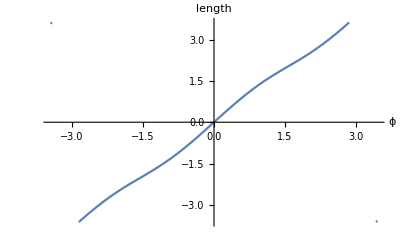

```mathematica
alphaTemp=50*π/180;
Plot[ArcLenIndef/.{ϕ->x,α->alphaTemp},{x,-1.1π,1.1π},PlotRange->All,AxesLabel->{"ϕ","length"}]
```

Difference to a very crude approx which may be easier to integerate
could be made better by some nested fitting

(1+0.02 α+0.18 α^2) ϕ

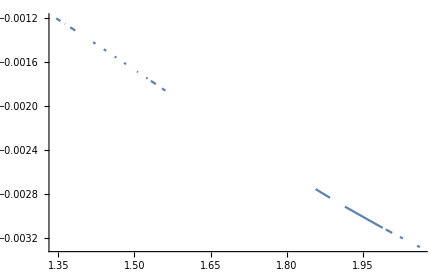

```mathematica
alphaTemp=5*π/180;
ArcLenIndefApprox=ϕ(1+α*0.02+α^2*0.18)
Plot[{(ArcLenIndef/.{ϕ->x,α->alphaTemp})-(ArcLenIndefApprox /.{ϕ->x,α->alphaTemp})},{x,-1.0π,1π},PlotRange->All]
```

Trying to keep between these discontinuities we chose -π<u<0 which also happens to be the range of the intersect coordinates under positive d displacement of the moving elipse

```mathematica
assum={α∈Reals,α>0,α<π/2,u<0,u>-π,d∈ Reals,d>0};
```

```mathematica
ArcLenIndef=Integrate[√((D[xpos[ϕ],ϕ])^2+(D[zpos[ϕ],ϕ])^2),ϕ]
```

(√(-(-6-2 Cos[2 α]+Cos[2 (α-ϕ)]-2 Cos[2 ϕ]+Cos[2 (α+ϕ)]) Sec[α]^2) (1/(√((Cos[α]+ⅈ Sin[α])^2))ⅈ (-2 Cos[α] EllipticF[ⅈ ArcSinh[√((Cos[α]+ⅈ Sin[α])^2) Tan[ϕ/2]],Cos[4 α]-ⅈ Sin[4 α]]+EllipticE[ⅈ ArcSinh[√((Cos[α]+ⅈ Sin[α])^2) Tan[ϕ/2]],Cos[4 α]-ⅈ Sin[4 α]] (Cos[α]+ⅈ Sin[α])) (Cos[α]+ⅈ Sin[α]) √(1+Cos[2 α] Tan[ϕ/2]^2-ⅈ Sin[2 α] Tan[ϕ/2]^2) √(1+Cos[2 α] Tan[ϕ/2]^2+ⅈ Sin[2 α] Tan[ϕ/2]^2)+Cos[ϕ/2]^2 (Tan[ϕ/2]+2 Cos[2 α] Tan[ϕ/2]^3+Tan[ϕ/2]^5)))/((1+Cos[ϕ]) √(-(-6-2 Cos[2 α]+Cos[2 (α-ϕ)]-2 Cos[2 ϕ]+Cos[2 (α+ϕ)])/(1+Cos[ϕ])^2) √(1+2 Cos[2 α] Tan[ϕ/2]^2+Tan[ϕ/2]^4))

Try to do the definite integral directly

```mathematica
ustart=Intersect1;
uend=Intersect2;
Integrate[√((xpos'[u])^2+(zpos'[u])^2),{u,ustart,uend},Assumptions->{assum,ustart<0,ustart>-π,uend<0,uend>-π}]
```

$Aborted

Try to do it manually

```mathematica
ArcLenDefApprox= (ArcLenIndefApprox/.ϕ->Intersect1)-(ArcLenIndefApprox/.ϕ->Intersect2);
ArcLenDefManual=(ArcLenIndef/.ϕ->Intersect1)-(ArcLenIndef/.ϕ->Intersect2);
```

Some bozo tests
For a cricle
First that the arc length is approx pi for d=0 α=0

```mathematica
alphaTemp=0*π/180;
ArcLenDefManual/.{α->alphaTemp,d->0.0001}
```

3.14149-4.44089×10^-16 ⅈ

```mathematica
Limit[ArcLenDefManual/.{α->alphaTemp},d->0]
```

$Aborted

```mathematica
FullSimplify[Simplify[ArcLenDefManual/.{α->alphaTemp,d->zmax[0]}]]
```

0

Now for a tilted case, the arc length should be half the circumference as d->0
lets try to check this numerically

```mathematica
alphaTemp=45*π/180;
N[cicumEllipse[alphaTemp]]
N[2*ArcLenDefManual/.{α->alphaTemp,d->0.000001*zmax[alphaTemp]}]
N[2*(ArcLenDefManual/.{α->alphaTemp,d->0.0000001*zmax[alphaTemp]})-cicumEllipse[alphaTemp]]
```

7.6404

7.64039-5.12×10^-10 ⅈ

-2.96353×10^-7-3.97047×10^-23 ⅈ

```mathematica
Limit[ArcLenDefManual/.α->0,d->0]
```

$Aborted

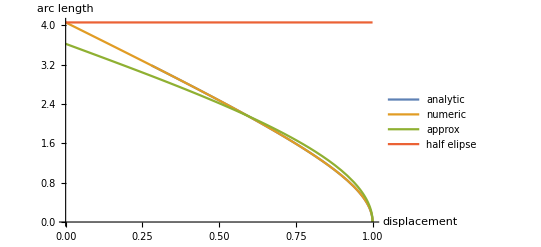

NIntegrate::nlim: u = ArcTan[-0.321394 √(9.68111-9.68111 x^2),-1. x] is not a valid limit of integration.

2.07057×10^-13-3.4544×10^-15 ⅈ

```mathematica
alphaTemp=50*π/180;
ArcLenNum[dvar_,αvar_]:=NIntegrate[(√((xpos'[u])^2+(zpos'[u])^2))/.{d->dvar,α->αvar},{u,Intersect2/.{d->dvar,α->αvar},Intersect1/.{d->dvar,α->αvar}}]
Plot[{ArcLenDefManual/.{d->x zmax[alphaTemp],α->alphaTemp},ArcLenNum[x zmax[alphaTemp],alphaTemp],ArcLenDefApprox/.{d->x zmax[alphaTemp],α->alphaTemp},1/2 cicumEllipse[alphaTemp]},{x,0,1},PlotLegends->{"analytic","numeric","approx","half elipse"},AxesLabel->{"displacement","arc length"}]
N[((ArcLenDefManual/.{d->x zmax[alphaTemp],α->alphaTemp})-(ArcLenNum[x *zmax[alphaTemp],alphaTemp]))/.x->0.5]
```

```mathematica
alphaTemp=45*π/180;
Manipulate[
b=bfac*zmax[alphaTemp];
Show[
ParametricPlot[{xpos[a],zpos[a]}/.α->alphaTemp,{a,-π,π},PlotLabel->StringForm["``.,``.",bfac,N[Re[ArcLenDefManual/.{α->alphaTemp,d->b}],2]],
PlotRange->{{-1.5,1.5},{-1,1}*zmax[alphaTemp]}],
ParametricPlot[{xpos[a],zpos[a]+b}/.α->alphaTemp,{a,-π,π}],
ParametricPlot[{xpos[a],zpos[a]+b}/.α->alphaTemp,{a,Intersect1/.{d->b,α->alphaTemp},Intersect2/.{d->b,α->alphaTemp}},PlotStyle->{Red}],
ListPlot[{{xpos[Intersect1],zpos[Intersect1]+d},{xpos[Intersect2],zpos[Intersect2]+d}}/.{α->alphaTemp,d->b},PlotStyle->Red,PlotMarkers->{Automatic, Medium}],
PlotRange->{{-1.1,1.1},zmax[alphaTemp]*{-0.7,0.8}}
],
{bfac,10^-6,0.99999}
]
```

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-q^2))/2,q/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-q^2))/2,q/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-q^2))/2,q/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[1/2 √(4-4 wfac^2),wfac] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[1/2 √(4-4 wfac^2),wfac] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[1/2 √(4-4 wfac^2),wfac] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ConditionalExpression[-0.453368+2 π 2,2∈] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ConditionalExpression[-0.453368+2 π 2,2∈] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ConditionalExpression[-0.453368+2 π 2,2∈] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value Intersect1 in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-zmax[alphaTemp],zmax[alphaTemp]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

ParametricPlot::plln: Limiting value ArcTan[(√(4-w^2))/2,-w/2] in {a,Intersect1/.{d→b,α→alphaTemp},Intersect2/.{d→b,α→alphaTemp}} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

## Areas

Find the ellipse area 
http://tutorial.math.lamar.edu/Classes/CalcII/ParaArea.aspx

from the plot above we can see that the integral of u from 0 to π will give half the area
Agrees with the simple expression calculated at the start

```mathematica
ELipseArea=4*Integrate[zpos[ϕ]*(xpos'[ϕ]),{ϕ,0,-π/2}]
FullSimplify[areaEllipse[α]]
```

π Sec[α]

π Sec[α]

```mathematica
alphaTemp=0*π/180;
NIntegrate[ArcLenDefManual/.α->alphaTemp,{d,0,zmax[alphaTemp]},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->10]
N[areaEllipse[alphaTemp]]
```

4.

3.14159

```mathematica
alphaTemp=0*π/180;
NIntegrate[ArcLenNum[d,alphaTemp],{d,0,zmax[alphaTemp]},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->10]
N[areaEllipse[alphaTemp]]
```

NIntegrate::nlim: u = ArcTan[-0.5 √(4.-1. d^2),-0.5 d] is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

4.

3.14159

```mathematica
Integrate[ArcLenDefManual,d]
```

$Aborted

0.859846-2.30481×10^-10 ⅈ

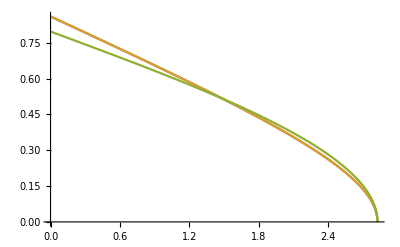

```mathematica
ProbDenAnal[dvar_,αvar_]:=(ArcLenDefManual/.{d->dvar,α->αvar})/(ELipseArea/.{α->αvar})
ProbDenApprox[dvar_,αvar_]:=(ArcLenDefApprox/.{d->dvar,α->αvar})/(ELipseArea/.{α->αvar});
ProbDenNum[dvar_,αvar_]:=ArcLenNum[dvar,αvar]/areaEllipse[αvar]
alphaTemp=45*π/180;
ProbDenAnal[0.000001,alphaTemp]
Plot[{ProbDenAnal[x,alphaTemp],ProbDenNum[x,alphaTemp],ProbDenApprox[x,alphaTemp]},{x,0,zmax[alphaTemp]}]
```

Check normalization

NIntegrate::nlim: u = ArcTan[-0.492404 √(4.12436-1. l^2),-0.492404 l] is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

1.27980687

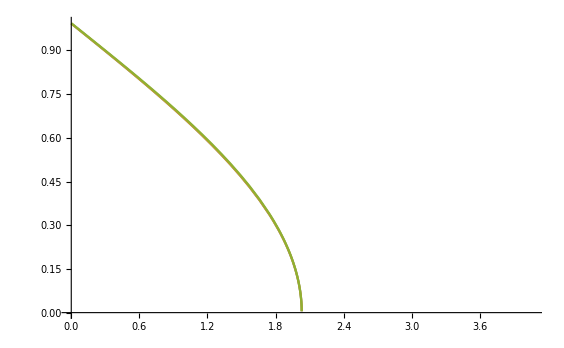

```mathematica
NIntegrate[ProbDenNum[l,alphaTemp],{l,0,1*zmax[alphaTemp]},AccuracyGoal->5,PrecisionGoal->5,WorkingPrecision->10]
```

```mathematica
NIntegrate[ProbDenAnal[l,alphaTemp],{l,0,2*zmax[alphaTemp]},WorkingPrecision->10]
NIntegrate[ProbDenApprox[l,alphaTemp],{l,0,2*zmax[alphaTemp]}]
```

1.279818182+1.140004317 ⅈ

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.28467+1.15859 ⅈ

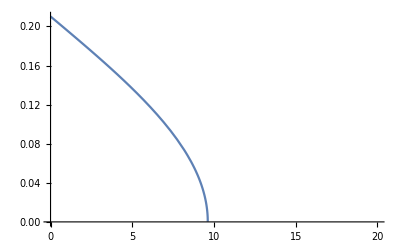

```mathematica
alphaTemp=12*π/180;
ProbDenLNum[lvar_,αvar_]:=ProbDenNum[lvar*Tan[αvar],αvar]*Tan[αvar];
Plot[ProbDenLNum[l,alphaTemp],{l,0,20}]
```

```mathematica
NIntegrate[ProbDenLNum[l,alphaTemp],{l,0,14}]
```

NIntegrate::nlim: u = ArcTan[-0.489074 √(4.18072-0.0451803 l^2),-0.103956 l] is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in l near {l} = {9.62478}. NIntegrate obtained 1.28276+0.35945 ⅈ and 4.42946×10^-6 for the integral and error estimates.

1.28276+0.35945 ⅈ

```mathematica
ArcLenDefManual>>"out.txt"
```

Now simplify down this big mess

```mathematica
ArcLenDefManual=Simplify[ArcLenDefManual,Assumptions->assum,TimeConstraint->6000,Trig->False]
ArcLenDefManual=Simplify[ArcLenDefManual,Assumptions->assum,TimeConstraint->6000]
```

Simplify::time: Time spent on a transformation exceeded 6000. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

```mathematica
SetDirectory[NotebookDirectory[]]
Save["arclen",ArcLenDefManual]
```

E:\Dropbox\UNI\project\programs\mcp_delay_sim_git

```mathematica
ArcLenDefManual=Simplify[Expand[ArcLenDefManual],Assumptions->assum]
```

The expression for this integral is way to big and it wont simplify down

```mathematica
IndefTotalArcLen=Integrate[ArcLenDefManual,d]
```

$Aborted

```mathematica
ProbDensity=ArcLenDefManual/ELipseArea;
```

-3.46815+4.18762×10^-15 ⅈ

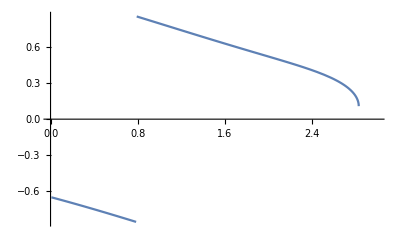

```mathematica
alphaTemp=45*π/180;
ArcLenDefManual/.{d->0.5,α->alphaTemp}
Plot[ProbDensity/.{d->x,α->alphaTemp},{x,0,3}]
```

```mathematica
ArcLenDefManual=Simplify[ArcLenDefManual,Assumptions->assum,TimeConstraint->6000]
```